# Stochastic processes

We examine a few stochastic processes, and practice with random variables.

```mathematica
ClearAll["Global`*"]
```

Generate a pseudorandom real number between 0 and 2π.

```mathematica
RandomReal[{0,2Pi}]
```

2.82534

#### Ideal square function

Given a solution whose points are contained in a rectangle [x_min,x_max]×[y_min,y_max], this function returns the ideal square.

```mathematica
IdealSquare[xMin_,xMax_,yMin_,yMax_]:=If[yMax-yMin≥xMax-xMin,
xMean=Mean[{xMin,xMax}];
dx=(yMax-yMin)/2;
{xMean-dx,xMean+dx,yMin,yMax},
yMean=Mean[{yMin,yMax}];
dy=(xMax-xMin)/2;
{xMin,xMax,yMean-dy,yMean+dy}
]
```

#### Random walk

We create a random walk function which takes in initial conditions, number of time-steps, and distance traveled per time-step.

```mathematica
RandomWalk[init_,steps_,distance_,OptionsPattern[{plot->True}]]:=Module[{},
solutions={init};
direction[]:=Module[{},t=RandomReal[{0,2Pi}];{{Cos[t]},{Sin[t]}}];

n=2;

(* To ensure that our final plot has a 1:1 coordinate ratio, we find the smallest and largest x and y values, respectively. *)
xMin=init[[1]];
xMax=init[[1]];
yMin=init[[2]];
yMax=init[[2]];

While[n≤steps,
curSol=solutions[[n-1]];
newSol=curSol+distance direction[];

(* xMin, xMax, yMin, yMax are re-evaluated at every iteration. *)
xMin=Min[xMin,newSol[[1]]];
xMax=Max[xMax,newSol[[1]]];
yMin=Min[yMin,newSol[[2]]];
yMax=Max[yMax,newSol[[2]]];
solutions=Append[solutions,newSol];
n+=1];

(* Calculate ideal square. *)
{xMin,xMax,yMin,yMax}=IdealSquare[xMin,xMax,yMin,yMax];

solutions=Level[solutions[[#]],{-1}]&/@Range[steps];
If[OptionValue[plot],
ListPlot[
solutions,Joined->True,AspectRatio->1,
PlotRange->{{xMin,xMax},{yMin,yMax}},
PlotStyle->Gray
],
solutions]
]
```

Running RandomWalk from the origin with 10,000 time-steps and step-distance 1.

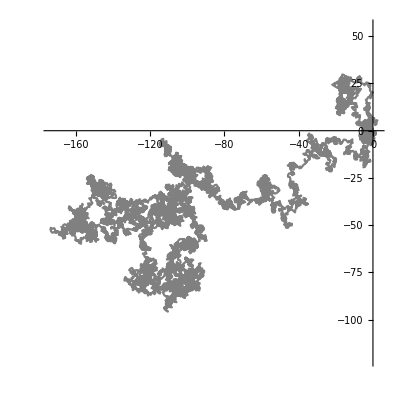

```mathematica
RandomWalk[{{0},{0}},10000,1]
```

```mathematica
Mean[{1,2}]
```

3/2